# The Breathless Line

Reviewed by Pavel Hajek.

Euclid describes a line as a "breadthless length". Every line we draw has some thickness; a line without breadth belongs to an idealized geometry. We ask whether such an ideal object can emerge from a discrete substrate: can a family of shortest paths, spread across a graph, concentrate on a straight segment as the graph is refined?

To make this precise, start with a graph G_0 embedded in ℝ^2 and specify how it is subdivided. For a triangular mesh, we can consider barycentric subdivision and write G_n=B^n(G_0). The original endpoints remain fixed, so a_n=a and b_n=b, while the minimal model l_n(a,b) may contain many shortest paths.

Each subdivision inherits an embedding. Counting the paths through each edge or vertex gives an occupation density. We ask whether its normalized measure converges weakly to uniform length on the straight segment [a,b], and how quickly its transverse spread vanishes.

The regular triangular tessellation provides a natural comparison: does it have the same convergence rate, or is it special in some way?

Instead of barycentric subdivision, we can also consider midpoint refinements of square and triangular grids.

For the hexagonal tessellation, we first need to decide what refinement should mean.

Now we will try to formulate the problem without a fixed embedding.

## Setup

Barycentric subdivision comes from the DiscreteGeometry paclet.

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
Needs["WolframInstitute`DiscreteGeometry`"]
```

## Paths and occupation

Let a,b be distinct vertices of a finite unweighted graph. Suppose there are N shortest paths between them, each with L edges.

Write c_E(e) for the number of these paths containing edge e, and c_V(v) for the number containing vertex v. Each path contributes L edge visits and L+1 vertex visits, so

∑_e c_E(e)=NL,    ∑_v c_V(v)=N(L+1)

For example, the two-square grid below has three shortest paths from a to b, each of length three. The edge labels are the occupation counts; they sum to nine.

```mathematica
With[
  {g = GridGraph[{2, 3}]},
  {counts = InfraMeasurement[g, InfraSegment[1, 6], "EdgeDensity"]},
  Graph[InfraSubstrateHighlight[g, {InfraSegment[1, 6] -> StandardBlue, {1, 6} -> StandardBlue}],
    EdgeLabels -> Normal @ KeyMap[UndirectedEdge @@ # &, counts], VertexLabels -> {1 -> Placed["a", Before], 6 -> Placed["b", After]}]]
```

-Graphics-

These counts give several probability distributions, depending on what we choose at random.

Choose a path uniformly. The probabilities that it contains a given edge or vertex are

q_E(e)=(c_E(e))/N,_V(v)=(c_V(v))/N.

These are occupation probabilities. They sum to L and L+1, respectively: one path occupies several edges and vertices. In particular, q_V(a)=q_V(b)=1.

Choose a location along that path. After choosing the path, choose one of its edges or vertices uniformly. The resulting distributions are

p_E(e)=(c_E(e))/NL,_V(v)=(c_V(v))/(N(L+1)).

Each sums to one. They describe where a randomly sampled edge visit or vertex visit occurs.

Observe the path at a fixed step. At step k, every shortest path occupies exactly one vertex at graph distance k from a. Thus

ρ_k(v)={(c_V(v))/N | d(a,v)=k
0 | otherwise,    ∑_v ρ_k(v)=1.

The vertex distribution above is their average:

p_V(v)=1/(L+1)∑_(k=0)^L ρ_k(v).

We can also choose uniformly from all edges—or all vertices—that occur in at least one shortest path. This gives equal weight to every occupied location, regardless of how many paths pass through it. It describes the support, while the distributions p_E and p_V retain the multiplicity of paths.

## The picture

Take growing neighborhoods of a center in the square, triangular and hexagonal tessellations. On the shell at half the graph radius, choose two vertices joined by many shortest paths: the first vertex of the shell, and the vertex of the shell with the most shortest paths from it.

Draw the whole graph using a spring-electric embedding. Translate, rotate and uniformly rescale this drawing so that the two selected vertices occupy the same positions at every size:

φ_n(v)=s_n R_n F_n(v)+t_n,_n(a_n)=(0,0),_n(b_n)=(1,0).

Here F_n is the spring-electric layout, R_n is a rotation, s_n is a positive scale, and t_n is a translation. The graph determines shortest paths; this embedding determines the geometric positions we compare.

The columns are square, triangular and hexagonal tessellations; sizes increase down the rows. The endpoints are fixed. Edge thickness is proportional to p_E, with the thickest edge set to the same display width in each panel.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = First @ GraphCenter[g]},
    {shell = Keys @ InfraMeasurement[g, InfraShell[c, Floor[GraphRadius[g]/2]], "VertexDensity"]},
    {a = First @ shell},
    {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
    {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {u = xy[b] - xy[a]},
    {aligned = (p |-> {u, Cross[u]} . (p - xy[a]) / (u . u)) /@ GraphEmbedding[g]},
    InfraSubstrateHighlight[Graph[g, VertexCoordinates -> aligned], {InfraSegment[a, b] -> StandardBlue, {a, b} -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}]
```

-Graphics-

The same construction on a triangulated mesh, from coarse to fine:

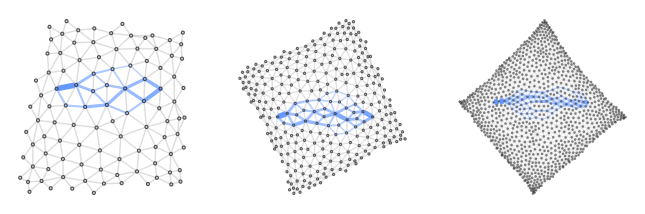

```mathematica
GraphicsRow @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
    {c = First @ GraphCenter[g]},
    {shell = Keys @ InfraMeasurement[g, InfraShell[c, Floor[GraphRadius[g]/2]], "VertexDensity"]},
    {a = First @ shell},
    {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
    {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {u = xy[b] - xy[a]},
    {aligned = (p |-> {u, Cross[u]} . (p - xy[a]) / (u . u)) /@ GraphEmbedding[g]},
    InfraSubstrateHighlight[Graph[g, VertexCoordinates -> aligned], {InfraSegment[a, b] -> StandardBlue, {a, b} -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}}]
```

Subdivision. Start with a square split along one diagonal and choose the two opposite corners off that diagonal. Barycentric subdivision splits every triangle into six. A vertex of the subdivision is a chain of faces, and an original corner stays the singleton chain at every level. Keep the original endpoints and draw each graph in its inherited embedding, aligned by the same rule.

```mathematica
GraphicsRow @ Table[
  With[
    {g = Nest[BarycentricRefinement, Graph[{1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 1, 1 <-> 3}], k]},
    {a = Nest[List, 2, k], b = Nest[List, 4, k]},
    {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {u = xy[b] - xy[a]},
    {aligned = (p |-> {u, Cross[u]} . (p - xy[a]) / (u . u)) /@ GraphEmbedding[g]},
    InfraSubstrateHighlight[Graph[g, VertexCoordinates -> aligned], {InfraSegment[a, b] -> StandardBlue, {a, b} -> StandardBlue}]],
  {k, {2, 3, 4}}]
```

-Graphics-

The panels show two, three and four subdivisions. All edges have unit cost. This is a nested refinement of one complex; the preceding tessellation panels are growing neighborhoods.

## A line takes shape

Place each edge probability at its embedded midpoint x_n(e). This gives a probability measure in the plane:

μ_n=∑_e p_(E,n)(e)δ_(x_n(e)).

Here δ_x is unit mass at x. The question is whether these measures approach uniform length on the fixed segment. Explicitly, do we have

∑_e p_(E,n)(e)f(x_n(e))→_0^1 f(t,0)dt?

The limit is required for every bounded continuous function f. It combines concentration across the line with uniform occupation along it.

We measure these two features separately. Write (X,Y) for a point sampled from μ_n. Its transverse spread and longitudinal discrepancy are

w_n=√(∫_(R^2) y^2 d μ_n(x,y)),_n=sup_t Abs[Pr (X≤t)-U(t)].

Here U is the distribution function of the uniform law on [0,1]. The left plot shows transverse spread; the right shows longitudinal discrepancy. The horizontal coordinate is the shell radius: on the large tessellations the radius grows, and the mesh is read at its three sizes.

```mathematica
With[
  {readouts = Join[
    Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate[name, "Large"])},
        {c = First @ GraphCenter[g], xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
        Table[
          With[
            {shell = Keys @ InfraMeasurement[g, InfraShell[c, r], "VertexDensity"]},
            {a = First @ shell},
            {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
            {density = InfraMeasurement[g, InfraSegment[a, b], "EdgeDensity"], u = xy[b] - xy[a]},
            {masses = Values[density] / Total[density],
             midpoints = (e |-> {u, Cross[u]} . (Mean @ Lookup[xy, List @@ e] - xy[a]) / (u . u)) /@ Keys[density]},
            {order = Ordering[midpoints[[All, 1]]]},
            {cumulative = Accumulate[masses[[order]]], positions = Clip[midpoints[[order, 1]], {0, 1}]},
            {{r, Sqrt[masses . midpoints[[All, 2]]^2]},
             {r, Max[Abs[cumulative - positions], Abs[cumulative - masses[[order]] - positions]]}}],
          {r, 2, Floor[GraphRadius[g]/2]}]],
      {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}],
    {Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
        {c = First @ GraphCenter[g], xy = AssociationThread[VertexList[g], GraphEmbedding[g]], r = Floor[GraphRadius[g]/2]},
        {shell = Keys @ InfraMeasurement[g, InfraShell[c, r], "VertexDensity"]},
        {a = First @ shell},
        {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
        {density = InfraMeasurement[g, InfraSegment[a, b], "EdgeDensity"], u = xy[b] - xy[a]},
        {masses = Values[density] / Total[density],
         midpoints = (e |-> {u, Cross[u]} . (Mean @ Lookup[xy, List @@ e] - xy[a]) / (u . u)) /@ Keys[density]},
        {order = Ordering[midpoints[[All, 1]]]},
        {cumulative = Accumulate[masses[[order]]], positions = Clip[midpoints[[order, 1]], {0, 1}]},
        {{r, Sqrt[masses . midpoints[[All, 2]]^2]},
         {r, Max[Abs[cumulative - positions], Abs[cumulative - masses[[order]] - positions]]}}],
      {size, {"Small", "Medium", "Large"}}]}]},
  GraphicsRow[{
    ListLinePlot[readouts[[All, All, 1]], PlotRange -> All, AxesLabel -> {Text["r"], Text["w"]},
      PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}],
    ListLinePlot[readouts[[All, All, 2]], PlotRange -> All, AxesLabel -> {Text["r"], Text["D"]},
      PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}]}]]
```

-Graphics-

Observation. Transverse spread decreases on every substrate. Longitudinal discrepancy decreases on the square and triangular tessellations and on the mesh; on the hexagonal tessellation both quantities alternate with the parity of the radius. These observations do not establish convergence.

Open question. Do both quantities tend to zero for this embedding procedure, and at what rates? These finite computations do not prove convergence or a power law.

In the barycentric example both quantities decrease, but slowly. Four subdivisions do not decide whether the limit is the straight segment.

## The triangle

Choose a third vertex on the same shell, as far as possible from the nearer endpoint. Keep one common spring-electric embedding for all three sides. A reflection puts the third vertex above the base.

Each side carries its own normalized occupation measure. The colors distinguish the three sides in the medium-size square, triangular and hexagonal substrates.

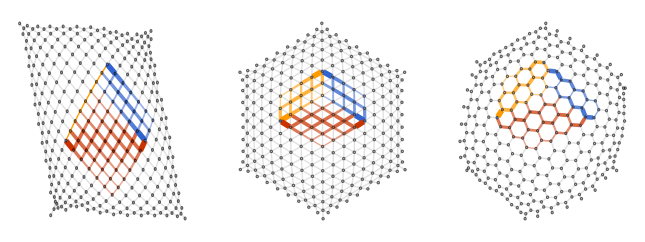

```mathematica
GraphicsRow @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Medium"])},
    {c = First @ GraphCenter[g]},
    {shell = Keys @ InfraMeasurement[g, InfraShell[c, Floor[GraphRadius[g]/2]], "VertexDensity"]},
    {a = First @ shell},
    {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
    {third = First @ MaximalBy[shell, Min[GraphDistance[g, #, a], GraphDistance[g, #, b]] &]},
    {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {u = xy[b] - xy[a]},
    {flip = {1, Sign[Cross[u] . (xy[third] - xy[a])]}},
    {aligned = (p |-> flip {u, Cross[u]} . (p - xy[a]) / (u . u)) /@ GraphEmbedding[g]},
    InfraSubstrateHighlight[Graph[g, VertexCoordinates -> aligned],
      {InfraSegment[a, b], InfraSegment[b, third], InfraSegment[third, a], {a, b, third} -> StandardBlue}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}]
```

## The triangle as one object

Give each side one third of the total mass:

μ_n^△=1/3(μ_n^ab+μ_n^bc+μ_n^ca).

Overlapping sides contribute additively. Normalizing each side before combining them prevents a side with more shortest paths from dominating solely through its path count.

The vertex density of each side is divided by its number of shortest paths, and the three are summed. A vertex is drawn the larger, the more mass it carries.

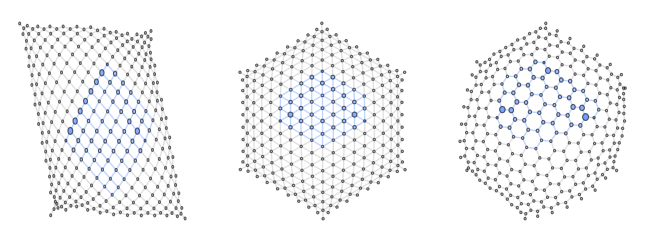

```mathematica
GraphicsRow @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Medium"])},
    {c = First @ GraphCenter[g]},
    {shell = Keys @ InfraMeasurement[g, InfraShell[c, Floor[GraphRadius[g]/2]], "VertexDensity"]},
    {a = First @ shell},
    {b = First @ MaximalBy[shell, InfraMeasurement[g, InfraSegment[a, #], "Cardinality"] &]},
    {third = First @ MaximalBy[shell, Min[GraphDistance[g, #, a], GraphDistance[g, #, b]] &]},
    {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {u = xy[b] - xy[a]},
    {flip = {1, Sign[Cross[u] . (xy[third] - xy[a])]}},
    {aligned = (p |-> flip {u, Cross[u]} . (p - xy[a]) / (u . u)) /@ GraphEmbedding[g]},
    {sides = {InfraSegment[a, b], InfraSegment[b, third], InfraSegment[third, a]}},
    InfraSubstrateHighlight[Graph[g, VertexCoordinates -> aligned],
      {Merge[(side |-> InfraMeasurement[g, side, "VertexDensity"] / InfraMeasurement[g, side, "Cardinality"]) /@ sides, Total] -> StandardBlue,
       {a, b, third} -> StandardBlue}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}]
```

If all three side measures converge to uniform measures on their limiting straight segments, their average converges to the corresponding triangle measure. This gives equal mass to each side; it equals normalized perimeter length only when the three side lengths agree.

The triangle asks whether several emerging lines fit together in the same drawing. Aligning its base fixes two corners; the position of the third remains an observed part of its shape.

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/BreathlessLineTutorial

### Keywords

line

triangle

shortest paths

occupation probability

weak convergence

tessellation

mesh

barycentric subdivision